# Technologie informacyjne i komunikacyjne

## Mathematica – zadania. Seria 4. Analiza.

Bartłomiej Zglinicki

Poniższe polecenie usuwa wszystkie istniejące definicje w bieżącej sesji programu Mathematica. Wydajemy je tutaj, by zapobiec ewentualnym konfliktom nazw w czasie wykonywania obliczeń.

```mathematica
Clear["Global`*"]
```

## Zadanie 13.

### a)

```mathematica
Limit[(n^100+n^99)^(1/100)-n,n->Infinity]
```

1/100

### b)

```mathematica
Limit[n^2 ((1+p/n)^q-(1+q/n)^p),n->Infinity]
```

-1/2 p (p-q) q

### c)

```mathematica
Limit[2^(-n) Product[1+i/n,{i,1,n}],n->Infinity]
```

0

### d)

```mathematica
Limit[Sum[i^5,{i,1,n}]/n^6,n->Infinity]
```

1/6

## Zadanie 14.

```mathematica
D[a x^5+(b+1) x^3+7 x+1,x]
```

7+3 (1+b) x^2+5 a x^4

## Zadanie 15.

```mathematica
f[x_]:= x^2 Cos[2 x]
```

```mathematica
D[f[x],{x,10}]
```

23040 Cos[2 x]-1024 x^2 Cos[2 x]-10240 x Sin[2 x]

```mathematica
% /. x->0
```

23040

## Zadanie 16.

### a)

```mathematica
Integrate[(x^2-2x+3) E^x,x]
```

ⅇ^x (7-4 x+x^2)

### b)

```mathematica
Integrate[Sqrt[x] Log[x]^2,x]
```

2/27 x^(3/2) (8-12 Log[x]+9 Log[x]^2)

### c)

```mathematica
Integrate[x^4/(x^2+1),x]
```

-x+x^3/3+ArcTan[x]

### d)

```mathematica
Integrate[1/(x+Sqrt[x-x^2]),x]
```

-ArcTan[(√(x-x^2))/x]-1/2 Log[-1+x]+Log[1-x+√(x-x^2)]

### e)

```mathematica
Integrate[Sqrt[E^(2 x)+2 E^x+4],x]
```

√(4+2 ⅇ^x+ⅇ^(2 x))+4 ArcTanh[ⅇ^x/2-1/2 √(4+2 ⅇ^x+ⅇ^(2 x))]-Log[-1-ⅇ^x+√(4+2 ⅇ^x+ⅇ^(2 x))]

## Zadanie 17.

### a)

```mathematica
Integrate[(x+1)/(x^2+1)^(3/2),{x,-Infinity,Infinity}]
```

2

### b)

```mathematica
Integrate[(x Log[x]^3)/(x^4+1),{x,-Infinity,Infinity}]
```

(13 ⅈ π^4)/64

## Zadanie 18.

### a)

```mathematica
Simplify[Laplacian[x/(x^2+y^2),{x,y}]]==0
```

True

### b)

```mathematica
Simplify[Laplacian[Sin[x] Cosh[y],{x,y}]]==0
```

True

### c)

```mathematica
Simplify[Laplacian[Log[x^2+y^2],{x, y}]]==0
```

True

## Zadanie 19.

### a)

```mathematica
Sum[k, {k, n}]
```

1/2 n (1+n)

### b)

```mathematica
Sum[k^2,{k, n}]
```

1/6 n (1+n) (1+2 n)

### c)

```mathematica
Sum[1/(k (k + 1) (k + 2)), {k, n}]
```

1/4-1/(2 (1+n) (2+n))

## Zadanie 20.

```mathematica
f[x_]:= 3 x + 12 / (1 + x)
```

### a)

#### i)

```mathematica
D[f[x],x]
```

3-12/(1+x)^2

#### ii)

```mathematica
Integrate[f[x],{x, 1, 3}]
```

12+Log[4096]

#### iii)

```mathematica
Series[f[x], {x, x0, 3}]
```

(3 x0+12/(1+x0))+(3-12/(1+x0)^2) (x-x0)+(12 (x-x0)^2)/(1+x0)^3-(12 (x-x0)^3)/(1+x0)^4+O[x-x0]^4

### b)

Tworzymy zmienną exX i przypisujemy do niej listę punktów stacjonarnych funkcji f(x) (czyli wartości x, dla których pochodna f’(x) znika). Parametr Reals zapewnia, że otrzymamy tylko rozwiązania rzeczywiste. Funkcja Values zamienia listę reguł w listę liczb. Funkcja Flatten zamienia listę zagnieżdżoną (listę list liczb) w listę “płaską” (listę liczb). Warto pobawić się tym poleceniem, usuwając różne jego elementy (przede wszystkim Values i Flatten) i obserwując, jak zmieni się wynik.

```mathematica
exX = Flatten[Values[Solve[D[f[x],x]==0,x,Reals]]]
```

{-3,1}

Tworzymy zmienną exY i przypisujemy do niej listę wartości funkcji f(x) w jej punktach stacjonarnych.

```mathematica
exY = f[exX]
```

{-15,9}

Tworzymy zmienną exXY zawierającą listę par {x, y}, gdzie x to kolejne punkty stacjonarne oraz y = f(x).

```mathematica
exXY = Transpose[{exX, exY}]
```

{{-3,-15},{1,9}}

### c)

```mathematica
Limit[f[x],x-> -1, Direction->1]
```

-∞

```mathematica
Limit[f[x], x-> -1, Direction-> -1]
```

∞

### d)

```mathematica
m = Limit[f[x]/x, x -> Infinity]
```

3

```mathematica
k = Limit[f[x] - m x, x -> Infinity]
```

0

```mathematica
asf[x_]:= m x + k
```

### e)

W rozwiązaniu będziemy ukrywać wyniki poleceń wykonujących kroki pośrednie - rysujących wykres samej funkcji, samych ekstremów oraz samej asymptoty, pisząc na ich końcu średnik (;). Naszym celem jest rysunek zawierający wszystkie te wykresy.

```mathematica
plotf = Plot[f[x], {x, -3, 5}, PlotStyle->Yellow, PlotLabel->Style[TraditionalForm[HoldForm[f[x] = 3 x + 12 / (1 + x)]],FontSize->14]];
```

```mathematica
plotEx = ListPlot[exXY, PlotStyle->{Blue, Large}];
```

```mathematica
plotAsymptote1 = ContourPlot[x==-1,{x,-3,5},{y,-100,100},ContourStyle->{Red, Dashed}];
```

```mathematica
plotAsymptote2 = Plot[asf[x], {x, -3, 5}, PlotStyle->{Red, Dashed}];
```

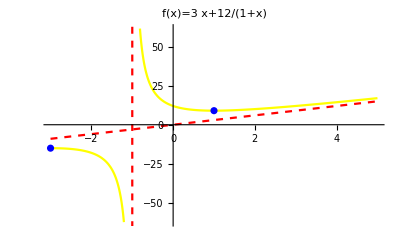

```mathematica
Show[plotf, plotEx, plotAsymptote1, plotAsymptote2]
```